## Model M/M/1 cd

## Rozkład czasu oczekiwania i przebywania

1. Rozważmy model M/M/1 z intensywnością strumienia wejściowego λ i intensywnością obsługi μ. 
(a) Wyznacz (symbolicznie) rozkład czasu przebywania zgłoszenia w systemie i czasu oczekiwania na obsługę. 
(b) Załóżmy, że λ=15/min. Aktualnie serwer jest w stanie obsłużyć 15.1 zgłoszenia w ciągu minuty. Jaki jest odsetek zgłoszeń, które będą musiały czekać na obsługę dłużej niż 5 min?
(c) Po narzekaniach użytkowników, postanowiono wymienić stary serwer na nowszy. Jaką intensywność obsługi powinien zapewnić nowy serwer, aby odsetek użytkowników czekających na rozpoczęcie obsługi dłużej niż 5 min nie przekroczył 0.01?

```mathematica
p = GeometricDistribution[1-ρ];
Erl[k_]=ErlangDistribution[k, µ];
Sdist = ParameterMixtureDistribution[Erl[k + 1], k\[Distributed]p];
PDF[Sdist, t]
```

Piecewise[{{-ⅇ^(t (-1+ρ) µ) (-1+ρ) µ, t>0}, {0, True}}]

```mathematica
S[t_]=Assuming[t ∈ Reals, Integrate[PDF[Sdist, x], {x, 0, t}]]
```

Piecewise[{{1-ⅇ^(t (-1+ρ) µ), t>0}, {0, True}}]

```mathematica
Str[s_]=LaplaceTransform[PDF[Sdist, t], t,s];
```

```mathematica
Btr[s_]=LaplaceTransform[PDF[ExponentialDistribution[µ], t], t,s];
Wtr[s_]=Str[s]/Btr[s] /.ρ->λ/µ
```

((λ-µ) (s+µ))/((-s+λ-µ) µ)

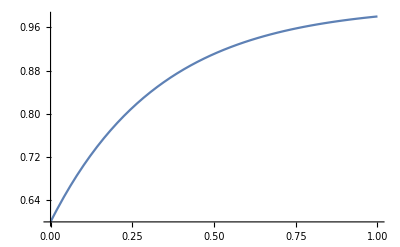

```mathematica
Wpdf[t_]=InverseLaplaceTransform[Wtr[s],s,t];
W[t_]= Integrate[Wpdf[x], {x,0,t}];
Plot[W[t]/.{λ->2,µ->5},{t,0,1}, PlotRange->All]
```

## Obsługa priorytetów

2. Serwer przyjmuje dwa typy zgłoszeń. Zgłoszenia tworzą strumień Poissona z intensywnościami λ_1 (typ 1) i λ_2 (typ 2). Obsługa dla każdego ze zgłoszeń ma rozkład wykładniczy z parametrem μ. Wyznacz średnie czasy oczekiwania i przebywania w systemie zgłoszeń każdego typu oraz ich średnią liczbę. Zbadaj wpływ parametrów wejściowych na te charakterystyki w przypadku gdy zgłoszenia typu pierwszego mają priorytet bezwzględny i względny nad zgłoszeniami typu drugiego.

## Model M/M/c

3. Zadania obsługiwane są przez c serwerów. Strumień wejściowy jest procesem Poissona o intensywności λ, a obsługa odbywa się z intensywnością μ. 
(a) Wyznacz stacjonarny rozkład liczby zadań w systemie dla c=10 . Zbadaj wpływ liczby serwerów na prawdopodobieństwo opóźnienia dla trzech wybranych obciążeń ρ. 
(b) Wyznacz rozkład liczby zajętych stanowisk dla c=15.

Do obliczeń przyda się pewna formuła. Okazuje się, że prawdopodobieństwo opóźnienia Π_W jest związane z prawdopodobieństwem B(c, ρ) utraty zgłoszenia w modelu M/M/c/c. Prawdopodobieństwo B(c, ρ) spełnia zależność rekurencyjną:
B(c,ρ)=(ρ B(c-1, ρ))/(c+ρ B(c-1,ρ)).
Przy pomocy tego wyrażenia możemy sprawnie wyznaczyć prawdopodobieństwo opóźnienia:
Π_W=(ρ B(c-1, cρ))/(1-ρ+ρB(c-1,cρ)).